```mathematica
tt = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {8, 0.6,0.1}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
ttb = {6759.969651,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/9},{9,0},{10,3/440},{11,1/60},{12,11/520},{13,9/560},{14,2/75},{15,33/640},{16,3/68},{17,19/360},{18,5/76},{19,31/400},{20,13/168},{21,81/880},{22,39/460},{23,7/64},{24,53/500},{25,121/1040},{26,16/135},{27,71/560},{28,17/116},{29,57/400},{30,187/1240},{31,181/1280},{32,67/440},{33,113/680},{34,59/350},{35,27/160},{36,133/740},{37,17/95},{38,73/390},{39,77/400},{40,31/164}}}
```

{6759.97,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/9},{9,0},{10,3/440},{11,1/60},{12,11/520},{13,9/560},{14,2/75},{15,33/640},{16,3/68},{17,19/360},{18,5/76},{19,31/400},{20,13/168},{21,81/880},{22,39/460},{23,7/64},{24,53/500},{25,121/1040},{26,16/135},{27,71/560},{28,17/116},{29,57/400},{30,187/1240},{31,181/1280},{32,67/440},{33,113/680},{34,59/350},{35,27/160},{36,133/740},{37,17/95},{38,73/390},{39,77/400},{40,31/164}}}

```mathematica
ll =  
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.6,0.1}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
llb = {3244.733812,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/72},{9,1/20},{10,3/88},{11,1/16},{12,4/65},{13,29/280},{14,13/120},{15,83/640},{16,77/680},{17,97/720},{18,14/95},{19,131/800},{20,19/120},{21,151/880},{22,167/920},{23,23/120},{24,97/500},{25,233/1040},{26,23/108},{27,253/1120},{28,9/40},{29,11/48},{30,153/620},{31,41/160},{32,17/66},{33,361/1360},{34,199/700},{35,19/72},{36,409/1480},{37,427/1520},{38,153/520},{39,471/1600},{40,47/164}}}
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{3244.73,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/72},{9,1/20},{10,3/88},{11,1/16},{12,4/65},{13,29/280},{14,13/120},{15,83/640},{16,77/680},{17,97/720},{18,14/95},{19,131/800},{20,19/120},{21,151/880},{22,167/920},{23,23/120},{24,97/500},{25,233/1040},{26,23/108},{27,253/1120},{28,9/40},{29,11/48},{30,153/620},{31,41/160},{32,17/66},{33,361/1360},{34,199/700},{35,19/72},{36,409/1480},{37,427/1520},{38,153/520},{39,471/1600},{40,47/164}}}

```mathematica
bb = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.6,0.05}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
bbb = {3131.958147,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/40},{9,13/400},{10,5/88},{11,43/480},{12,5/52},{13,57/560},{14,29/200},{15,9/64},{16,103/680},{17,131/720},{18,37/190},{19,169/800},{20,41/210},{21,39/176},{22,51/230},{23,229/960},{24,253/1000},{25,257/1040},{26,71/270},{27,15/56},{28,81/290},{29,29/100},{30,379/1240},{31,379/1280},{32,67/220},{33,417/1360},{34,11/35},{35,463/1440},{36,243/740},{37,123/380},{38,22/65},{39,271/800},{40,579/1640}}}
```

{3131.96,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/40},{9,13/400},{10,5/88},{11,43/480},{12,5/52},{13,57/560},{14,29/200},{15,9/64},{16,103/680},{17,131/720},{18,37/190},{19,169/800},{20,41/210},{21,39/176},{22,51/230},{23,229/960},{24,253/1000},{25,257/1040},{26,71/270},{27,15/56},{28,81/290},{29,29/100},{30,379/1240},{31,379/1280},{32,67/220},{33,417/1360},{34,11/35},{35,463/1440},{36,243/740},{37,123/380},{38,22/65},{39,271/800},{40,579/1640}}}

```mathematica
cc = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.8, 0.1}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
ccb = {3254.600866,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/72},{9,1/25},{10,3/88},{11,23/480},{12,33/520},{13,53/560},{14,11/100},{15,9/80},{16,93/680},{17,103/720},{18,99/760},{19,61/400},{20,131/840},{21,15/88},{22,21/115},{23,97/480},{24,53/250},{25,219/1040},{26,251/1080},{27,8/35},{28,141/580},{29,99/400},{30,307/1240},{31,1/4},{32,14/55},{33,89/340},{34,367/1400},{35,77/288},{36,413/1480},{37,431/1520},{38,17/60},{39,233/800},{40,503/1640}}}
```

{3254.6,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/72},{9,1/25},{10,3/88},{11,23/480},{12,33/520},{13,53/560},{14,11/100},{15,9/80},{16,93/680},{17,103/720},{18,99/760},{19,61/400},{20,131/840},{21,15/88},{22,21/115},{23,97/480},{24,53/250},{25,219/1040},{26,251/1080},{27,8/35},{28,141/580},{29,99/400},{30,307/1240},{31,1/4},{32,14/55},{33,89/340},{34,367/1400},{35,77/288},{36,413/1480},{37,431/1520},{38,17/60},{39,233/800},{40,503/1640}}}

```mathematica
dd = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {4, 0.8, 0.1}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
ddb = {2315.564622,{{2,0},{3,0},{4,0},{5,0},{6,1/70},{7,7/160},{8,29/360},{9,41/400},{10,51/440},{11,83/480},{12,12/65},{13,23/112},{14,16/75},{15,73/320},{16,15/68},{17,35/144},{18,97/380},{19,109/400},{20,11/40},{21,7/22},{22,303/920},{23,77/240},{24,173/500},{25,35/104},{26,187/540},{27,53/160},{28,53/145},{29,461/1200},{30,471/1240},{31,499/1280},{32,177/440},{33,557/1360},{34,29/70},{35,61/144},{36,637/1480},{37,653/1520},{38,659/1560},{39,349/800},{40,18/41}}}
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{2315.56,{{2,0},{3,0},{4,0},{5,0},{6,1/70},{7,7/160},{8,29/360},{9,41/400},{10,51/440},{11,83/480},{12,12/65},{13,23/112},{14,16/75},{15,73/320},{16,15/68},{17,35/144},{18,97/380},{19,109/400},{20,11/40},{21,7/22},{22,303/920},{23,77/240},{24,173/500},{25,35/104},{26,187/540},{27,53/160},{28,53/145},{29,461/1200},{30,471/1240},{31,499/1280},{32,177/440},{33,557/1360},{34,29/70},{35,61/144},{36,637/1480},{37,653/1520},{38,659/1560},{39,349/800},{40,18/41}}}

```mathematica
ee = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {4, 0.6, 0.1}, 4], 40
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

```mathematica
eeb = {2343.032263,{{2,0},{3,0},{4,0},{5,0},{6,1/70},{7,1/40},{8,7/90},{9,39/400},{10,31/220},{11,23/160},{12,7/40},{13,27/140},{14,67/300},{15,77/320},{16,19/85},{17,37/144},{18,21/76},{19,43/160},{20,61/210},{21,241/880},{22,143/460},{23,77/240},{24,163/500},{25,73/208},{26,377/1080},{27,409/1120},{28,209/580},{29,461/1200},{30,463/1240},{31,31/80},{32,529/1320},{33,107/272},{34,81/200},{35,49/120},{36,327/740},{37,317/760},{38,229/520},{39,141/320},{40,733/1640}}}
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{2343.03,{{2,0},{3,0},{4,0},{5,0},{6,1/70},{7,1/40},{8,7/90},{9,39/400},{10,31/220},{11,23/160},{12,7/40},{13,27/140},{14,67/300},{15,77/320},{16,19/85},{17,37/144},{18,21/76},{19,43/160},{20,61/210},{21,241/880},{22,143/460},{23,77/240},{24,163/500},{25,73/208},{26,377/1080},{27,409/1120},{28,209/580},{29,461/1200},{30,463/1240},{31,31/80},{32,529/1320},{33,107/272},{34,81/200},{35,49/120},{36,327/740},{37,317/760},{38,229/520},{39,141/320},{40,733/1640}}}

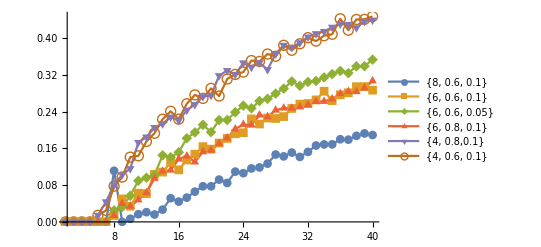

```mathematica
ListPlot[{tt[[2]],ll[[2]], bb[[2]], cc[[2]], dd[[2]], ee[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{"{8, 0.6, 0.1}", "{6, 0.6, 0.1}", "{6, 0.6, 0.05}", "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}"}]
```